```mathematica
Quit
```

# Examples of Multi-Field Vacuum Decay

This tutorial contains examples of false vacuum decay in potential with multiple scalar fields computed with Polygonal Bounces approach.

Loads the package

```mathematica
SetDirectory[FileNameTake[NotebookDirectory[],{1,-4}]];
<<"FindBounce.m"
```

## False vacuum decay

## Exact Solution: Quartic Potential

### Potential

```mathematica
Module[{ϵ = 1,Vt=5,ϕm=10,Vm=-20,ϕp=-5,Vp,ΔVp,ΔVm,α,Δ,Rt,A},
	Vp = -18+(ϵ-1)*3;
	ΔVm=Vt-Vm;
	ΔVp= Vt - Vp;
	α = -ϕp/ϕm;
	Δ = ΔVp/ΔVm;
	Rt = Sqrt[2 (1 + α)(α+Δ)]/(1 - Δ)ϕm/Sqrt[Vm];
	A = (1 + Sqrt[1 + 2 ΔVp Rt^2/ϕp^2])/( ΔVp Rt^2/ϕp^3);
	Extrema ={ϕp,0,ϕm} ;
	U[ϕ_] :=Piecewise[{{(Vp + ΔVp/ϕp^4 (ϕ-ϕp)^4)-Vp ,ϕ<0},{(Vm+  ΔVm/ϕm^4 (ϕ-ϕm)^4)-Vp,ϕ≥ 0}}];
	ActionExact =((2 π^2 ϕm^4)/(3ΔVm)) (4 α^3 + 6 α^2 Δ + 4α Δ^2+Δ^3+α^4(3+Δ(Δ -3)))/(1 - Δ)^3;
];
```

```mathematica
plotU = Plot[U[Extrema[[3]]-ϕ],{ϕ,0,Abs@Extrema[[1]]+Abs@Extrema[[3]]},
	PlotStyle->{Black,Dashed},
	Frame->True,
	FrameLabel->{"φ","V(φ)"},
	LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],
	GridLines->Automatic,
	GridLinesStyle->GrayLevel[.85],	
	ImageSize->Medium,	
	PlotRange->All,
	Axes->False
];
```

### Bounce

```mathematica
PBDefault =  FindBounce[ U[ϕ],{ϕ},{Extrema[[1]],Extrema[[3]]},"InitialFieldValue"->Extrema[[2]],"MethodSegmentation"->"HSPlus","Improvement"->False]
PB200 =  FindBounce[ U[ϕ],{ϕ},{Extrema[[1]],Extrema[[3]]},"InitialFieldValue"->Extrema[[2]],"Segments"->200,"MethodSegmentation"->"HSPlus","Improvement"->False]
Row[{"Exact Action = ",N@ActionExact}]
(*"Improvement"->False is needed since the second derivative is not well defined.*)
```

7
BounceFunction[<|Action -> 2.35359 10 , Bounce -> (Piecewise[{<<29>>}, -5.] & ), <<11>>, Radii -> {0.501859, 0.866284, 28.8076, 38.746, 42.9499, 46.551, 48.3364, 49.3943, 50.0926, 50.5878, 50.9571, 51.243, 51.4709, 51.6567, 51.8112, 51.8793, 51.942, 52., 52.0539, 52.1022, 52.1573, 52.2209, 52.2949, 52.4843, 52.7648, 53.2218, 54.0913, 54.9757, 56.6314, 60.6723, 80.8933}|>]

7
BounceFunction[<|Action -> 2.27367 10 , <<12>>, Radii -> {0.278164, 0.291649, 0.307307, 0.325792, 0.348071, 0.37565, 0.411031, 0.458757, 0.528214, 0.643253, 0.894382, 2.9735, 14.7282, 20.409, 24.2425, 27.131, 29.4272, 31.3141, 32.9009, 34.2585, 35.4361, 36.4689, 37.3831, <<167>>, 58.0246, 58.7617, 59.6686, 60.8117, 62.2972, 64.3062, 67.1748, 71.6044, 79.3426, 96.361, 197.072}|>]

Exact Action = 2.27175×10^7

### Plot

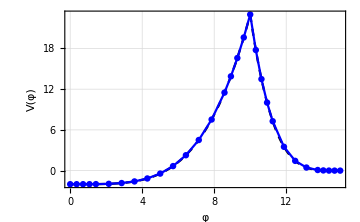
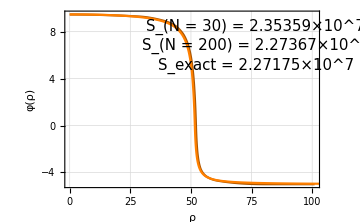

```mathematica
plot1 ={Show[plotU,ListPlot[Transpose@{PBDefault["PathLongitudinal"],PBDefault["Potential"]},Joined->True,Mesh->All,PlotStyle->Blue]],Show[{BouncePlot[PBDefault,PlotStyle->Darker@Orange],BouncePlot[PB200]},ImageSize->Medium,Epilog->{Text[Style[Row[{"S_(N = 30) = ",PBDefault["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.91}],Background->LightGreen],
Text[Style[Row[{"S_(N = 200) = ",PB200["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.8}],Background->LightGreen],
Text[Style[Row[{"S_exact = ",N@ActionExact}],10,15,"Times New Roman"],Scaled[{0.75,0.69}],Background->LightRed]}]};
Row[{plot1[[1]],plot1[[2]]}]
```

## Single Field Potential

### Potential

```mathematica
U1[ϕ_]:=Block[{αs = .9,V},V = 1/2(ϕ)^2-1/2(ϕ)^3+αs/8 (ϕ)^4 ];
Extrema1=Block[{φ},φ/.Sort@NSolve[(D[U1[φ],φ])==0,φ]];
plotU = Plot[U1[Extrema1[[3]]-ϕ],{ϕ,0,Extrema1[[3]]},
	PlotStyle->{Black,Dashed},
	Frame->True,
	FrameLabel->{"φ","V(φ)"},
	LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],
	GridLines->Automatic,
	GridLinesStyle->GrayLevel[.85],	
	ImageSize->Medium,	
	PlotRange->All,
	Axes->False];
```

### Bounce

```mathematica
PB1 =  FindBounce[ U1[ϕ],{ϕ},{Extrema1[[1]],Extrema1[[3]]},  "Segments"->10]
```

53.2553               2                                       230.044               2                            609.48               2
BounceFunction[<|Action -> 8063.93, Bounce -> (Piecewise[{{2.41202, #1 < 7.15393}, {4.49317 - ------- - 0.0203321 #1 , 7.15393 <= #1 < 9.08044}, {8.78132 - ------- - 0.0463353 #1 , <<1>>}, <<7>>, {-5.3262 + ------ + 0.0116363 #1 , 13.022 <= #1 < 15.1282}}] & ), <<11>>, Radii -> {7.15393, 9.08044, 9.81512, 10.3036, 10.7028, 11.0683, 11.4331, 11.8296, 12.3113, 13.022, 15.1282}|>]
                                                                                                  2                                                             2                                                 2
                                                                                                #1                                                            #1                                                #1

### Plot

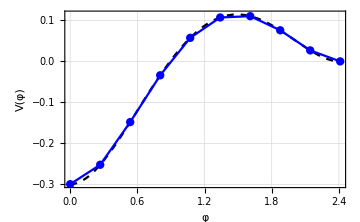
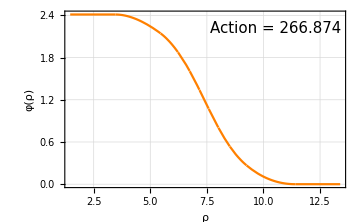

```mathematica
plot1 ={Show[plotU,ListPlot[Transpose@{PB1["PathLongitudinal"],PB1["Potential"]},Joined->True,Mesh->All,PlotStyle->Blue]],BouncePlot[PB1,ImageSize->Medium,Epilog->{Text[Style[Row[{"Action = ",PB1["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightGreen]}]};
Row[{plot1[[1]],plot1[[2]]}]
```

## Two Field Potential

### Potential

```mathematica
μλαϵ={{80.,100.},{.1,.3},2.,{0.,0.}} ;
rangeU={-16000,1000};
Extrema2 = {{0,12.9099},{6.25901,6.00687},{20.,0.}};
Potential2[ϕ_]:=Sum[-μλαϵ[[1,i]] (ϕ[[i]])^2 +μλαϵ[[2,i]](ϕ[[i]])^4+μλαϵ[[4,i]]ϕ[[i]] ,{i,1,2}]+ μλαϵ[[3]](ϕ[[1]])^2 (ϕ[[2]])^2; 
φs2 = {φ1,φ2};
contourV = ContourPlot[ Potential2[{ϕ1,ϕ2}],{ϕ1,-1,21},{ϕ2,-1,Extrema2[[1,2]]+1},PlotRange->rangeU,ContourShading->None,GridLines->Automatic,Contours->50,GridLinesStyle->Directive[Dashed,GrayLevel[.85]],ContourStyle->Opacity[0.4],FrameLabel->{"φ_1","φ_2"},ImageSize->400,LabelStyle->Directive[Black,FontSize->25, FontFamily->"Times New Roman",FontSlant->Plain] ];
```

### Bounce

```mathematica
Block[{time},
{time,PB2} =FindBounce[Potential2[φs2],{φ1,φ2},Extrema2[[{1,3}]],"InitialFieldValue"->Extrema2[[2]]]//AbsoluteTiming;
Row[{"Total time consumed = ",time," s."}]  ]
PB2
```

Total time consumed = 0.116198 s.

1.70257             2            0.427574             2                                          8.36201             2             2.95226             2                                           13.3053            2             7.48081             2                                           17.2221             2             12.5742             2                                          19.9915             2             17.612            2                                           21.5251             2             22.0793             2                                         21.7706             2             25.5978             2                                          20.7127             2             27.9052             2                                           18.3741             2             28.8375            2                                           14.8148             2             28.3151             2                                           10.1311             2             26.3316             2                                           4.45336             2             22.9447             2                                          2.05653             2             18.268             2                                          9.20833             2             12.4636            2                                           16.7873             2             5.73514             2                                            24.5586             2             1.67956             2                                           32.2722            2            9.51504             2                                           39.668             2            17.4856             2                                            46.483            2            25.2934             2                                            52.4604             2            32.6397             2                                           57.3568             2            39.2357             2                                            60.9407             2            44.8022             2                                           62.988             2            49.0654             2                                            63.2782             2            51.7533             2                                            61.5899             2            52.5883             2                                            57.6903             2            51.2738             2                                           51.3174             2           47.4682             2                                            42.1427             2            40.7253             2                                            29.6759             2            30.332             2                                           12.8887             2            14.0746             2
BounceFunction[<|Action -> 4952.69, BounceParameters -> {{{33.4865, -2.8395}, {66.529, -15.3664}, {88.4917, -35.4862}, {104.802, -56.6955}, {115.81, -76.7215}, {121.687, -93.8409}, {122.6, -106.919}, {118.77, -115.271}, {110.503, -118.567}, {98.1873, -116.759}, {82.3007, -110.032}, {63.3996, -98.7566}, {42.1107, -83.4628}, {19.1196, -64.8034}, {-4.8431, -43.5298}, {-29.0168, -20.4653}, {-52.6276, 3.51877}, {-74.9057, 27.5282}, {-95.1063, 50.6714}, {-112.537, 72.0944}, {-126.58, 91.0112}, {-136.683, 106.702}, {-142.35, 118.505}, {-143.138, 125.804}, {-138.648, 128.025}, {-128.514, 124.609}, {-112.39, 114.98}, {-89.9124, 98.4607}, {-60.6335, 74.0515}, {-23.697, 38.2806}}, {{-26.7024, 4.56792}, {-67.6896, 20.1067}, {-92.084, 42.4544}, {-109.063, 64.5337}, {-120.003, 84.435}, {-125.634, 100.836}, {-126.481, 112.989}, {-123.016, 120.547}, {-115.709, 123.46}, {-105.056, 121.896}, {-91.5846, 116.191}, {-75.8542, 106.808}, {-58.4492, 94.3042}, {-39.9717, 79.308}, {-21.0309, 62.4926}, {-2.23194, 44.5564}, {15.836, 26.2028}, {32.6128, 8.12209}, {47.582, -9.02763}, {60.2899, -24.6459}, {70.3581, -38.2089}, {77.4778, -49.2669}, {81.4003, -57.4354}, {81.9355, -62.3912}, {78.9499, -63.8677}, {72.3665, -61.6487}, {62.1669, -55.5579}, {48.3999, -45.4399}, {31.2091, -31.1083}, {10.8914, -11.4318}}, {{-1.70257, 0.427574}, {-8.36201, 2.95226}, {-13.3053, 7.48081}, {-17.2221, 12.5742}, {-19.9915, 17.612}, {-21.5251, 22.0793}, {-21.7706, 25.5978}, {-20.7127, 27.9052}, {-18.3741, 28.8375}, {-14.8148, 28.3151}, {-10.1311, 26.3316}, {-4.45336, 22.9447}, {2.05653, 18.268}, {9.20833, 12.4636}, {16.7873, 5.73514}, {24.5586, -1.67956}, {32.2722, -9.51504}, {39.668, -17.4856}, {46.483, -25.2934}, {52.4604, -32.6397}, {57.3568, -39.2357}, {60.9407, -44.8022}, {62.988, -49.0654}, {63.2782, -51.7533}, {61.5899, -52.5883}, {57.6903, -51.2738}, {51.3174, -47.4682}, {42.1427, -40.7253}, {29.6759, -30.332}, {12.8887, -14.0746}}, 1, {0.507235, 0.636166, 0.671688, 0.693599, 0.709783, 0.722825, 0.733901, 0.743645, 0.752443, 0.760548, 0.768136, 0.775336, 0.78225, 0.788957, 0.795525, 0.802015, 0.80848, 0.814974, 0.821548, 0.828259, 0.835177, 0.842389, 0.850013, 0.858201, 0.867171, 0.877254, 0.888988, 0.903362, 0.922525, 0.952795, 1.04686}}, Dimensions -> 4, Domain -> {0.507235, 1.04686}, InitialSegment -> 1, ImprovedBounce -> {-51.7767, {279.191, 253.615, 229.106, 195.637, 152.857, 103.391, 50.4408, -3.04732, -54.6278, -102.367, -144.78, -180.754, -209.478, -230.39, -243.136, -247.535, -243.565, -231.343, -211.118, -183.246, -148.137, -106.226, -57.9699, -3.8377, 55.6895, 120.117, 188.926, 261.532, 339.132, 410.46, 0}, {255.999, 889.434, 1275.92, 1447., 1364.8, 1044., 547.469, -32.8579, -596.966, -1054.46, -1337.12, -1406.22, -1255.01, -907.327, -412.83, 160.034, 732.699, 1225.9, 1569.11, 1709.03, 1615.76, 1286.17, 745.815, 49.5581, -718.877, -1448.28, -2001.87, -2219.26, -1928.82, -851.104, 0}, {-26.208, -16.3734, -13.6113, -11.1141, -8.45682, -5.62691, -2.71613, 0.162894, 2.90394, 5.41558, 7.62292, 9.46723, 10.9048, 11.9061, 12.4547, 12.5467, 12.1903, 11.4058, 10.226, 8.70261, 6.89057, 4.8355, 2.58053, 0.166951, -2.36618, -4.98235, -7.64811, -10.3348, -13.1041, -16.2411, 0}, {8.71413, 61.171, 101.21, 124.717, 123.653, 96.8357, 50.4997, -3.52901, -50.6826, -76.6115, -69.7434, -23.1861, 64.1232, 187.038, 334.549, 490.788, 636.582, 751.44, 815.808, 813.4, 733.142, 570.672, 329.695, 23.2515, -324.978, -679.069, -988.336, -1182.34, -1165.06, -714.046, 0}, {-0.0855933, -0.00321645, -0.00304981, -0.00301668, -0.00299347, -0.0029729, -0.00295406, -0.0029366, -0.00292022, -0.00290466, -0.00288972, -0.00287521, -0.00286096, -0.00284682, -0.00283265, -0.00281827, -0.00280352, -0.0027882, -0.00277204, -0.00275473, -0.00273581, -0.00271464, -0.00269021, -0.00266086, -0.00262366, -0.00257286, -0.00249572, -0.00235832, -0.00204061, -0.000814096, 0.0289349}}, Iterations -> 3, Segments -> 30, Method -> DerrickFindRoot, Path -> {{20., 0}, {18.4994, 0.0625173}, {17.4823, 0.243113}, {16.5617, 0.479845}, {15.6987, 0.765249}, {14.8756, 1.09101}, {14.0826, 1.45063}, {13.3135, 1.83896}, {12.5644, 2.25173}, {11.8327, 2.68534}, {11.1166, 3.13668}, {10.415, 3.60298}, {9.7272, 4.08172}, {9.05285, 4.5706}, {8.39192, 5.06744}, {7.74462, 5.57018}, {7.11135, 6.0768}, {6.49275, 6.58534}, {5.88963, 7.09378}, {5.30295, 7.60017}, {4.73326, 8.103}, {4.18056, 8.60141}, {3.6448, 9.0948}, {3.12596, 9.58274}, {2.62405, 10.065}, {2.1392, 10.5415}, {1.6717, 11.0126}, {1.22211, 11.4788}, {0.791555, 11.9419}, {0.382453, 12.4054}, {0, 12.9099}}, PathLongitudinal -> {0, 1.50194, 2.53489, 3.48546, 4.39441, 5.27961, 6.15039, 7.01196, 7.86724, 8.71778, 9.56423, 10.4067, 11.2447, 12.0776, 12.9045, 13.7241, 14.535, 15.3358, 16.1247, 16.8997, 17.6595, 18.4038, 19.1321, 19.8443, 20.5404, 21.2202, 21.8839, 22.5316, 23.1639, 23.7821, 24.4152}, Bounce -> (Piecewise[{{{20., 0}, #1 < 0.507235}, {{33.4865 - ------- - 26.7024 #1 , -2.8395 + -------- + 4.56792 #1 }, 0.507235 <= #1 < 0.636166}, {{66.529 - ------- - 67.6896 #1 , -15.3664 + ------- + 20.1067 #1 }, 0.636166 <= #1 < 0.671688}, {{88.4917 - ------- - 92.084 #1 , -35.4862 + ------- + 42.4544 #1 }, 0.671688 <= #1 < 0.693599}, {{104.802 - ------- - 109.063 #1 , -56.6955 + ------- + 64.5337 #1 }, 0.693599 <= #1 < 0.709783}, {{115.81 - ------- - 120.003 #1 , -76.7215 + ------ + 84.435 #1 }, 0.709783 <= #1 < 0.722825}, {{121.687 - ------- - 125.634 #1 , -93.8409 + ------- + 100.836 #1 }, 0.722825 <= #1 < 0.733901}, {{122.6 - ------- - 126.481 #1 , -106.919 + ------- + 112.989 #1 }, 0.733901 <= #1 < 0.743645}, {{118.77 - ------- - 123.016 #1 , -115.271 + ------- + 120.547 #1 }, 0.743645 <= #1 < 0.752443}, {{110.503 - ------- - 115.709 #1 , -118.567 + ------- + 123.46 #1 }, 0.752443 <= #1 < 0.760548}, {{98.1873 - ------- - 105.056 #1 , -116.759 + ------- + 121.896 #1 }, 0.760548 <= #1 < 0.768136}, {{82.3007 - ------- - 91.5846 #1 , -110.032 + ------- + 116.191 #1 }, 0.768136 <= #1 < 0.775336}, {{63.3996 - ------- - 75.8542 #1 , -98.7566 + ------- + 106.808 #1 }, 0.775336 <= #1 < 0.78225}, {{42.1107 + ------- - 58.4492 #1 , -83.4628 + ------ + 94.3042 #1 }, 0.78225 <= #1 < 0.788957}, {{19.1196 + ------- - 39.9717 #1 , -64.8034 + ------- + 79.308 #1 }, 0.788957 <= #1 < 0.795525}, {{-4.8431 + ------- - 21.0309 #1 , -43.5298 + ------- + 62.4926 #1 }, 0.795525 <= #1 < 0.802015}, {{-29.0168 + ------- - 2.23194 #1 , -20.4653 - ------- + 44.5564 #1 }, 0.802015 <= #1 < 0.80848}, {{-52.6276 + ------- + 15.836 #1 , 3.51877 - ------- + 26.2028 #1 }, 0.80848 <= #1 < 0.814974}, {{-74.9057 + ------ + 32.6128 #1 , 27.5282 - ------- + 8.12209 #1 }, 0.814974 <= #1 < 0.821548}, {{-95.1063 + ------ + 47.582 #1 , 50.6714 - ------- - 9.02763 #1 }, 0.821548 <= #1 < 0.828259}, {{-112.537 + ------- + 60.2899 #1 , 72.0944 - ------- - 24.6459 #1 }, 0.828259 <= #1 < 0.835177}, {{-126.58 + ------- + 70.3581 #1 , 91.0112 - ------- - 38.2089 #1 }, 0.835177 <= #1 < 0.842389}, {{-136.683 + ------- + 77.4778 #1 , 106.702 - ------- - 49.2669 #1 }, 0.842389 <= #1 < 0.850013}, {{-142.35 + ------ + 81.4003 #1 , 118.505 - ------- - 57.4354 #1 }, 0.850013 <= #1 < 0.858201}, {{-143.138 + ------- + 81.9355 #1 , 125.804 - ------- - 62.3912 #1 }, 0.858201 <= #1 < 0.867171}, {{-138.648 + ------- + 78.9499 #1 , 128.025 - ------- - 63.8677 #1 }, 0.867171 <= #1 < 0.877254}, {{-128.514 + ------- + 72.3665 #1 , 124.609 - ------- - 61.6487 #1 }, 0.877254 <= #1 < 0.888988}, {{-112.39 + ------- + 62.1669 #1 , 114.98 - ------- - 55.5579 #1 }, 0.888988 <= #1 < 0.903362}, {{-89.9124 + ------- + 48.3999 #1 , 98.4607 - ------- - 45.4399 #1 }, 0.903362 <= #1 < 0.922525}, {{-60.6335 + ------- + 31.2091 #1 , 74.0515 - ------ - 31.1083 #1 }, 0.922525 <= #1 < 0.952795}, {{-23.697 + ------- + 10.8914 #1 , 38.2806 - ------- - 11.4318 #1 }, 0.952795 <= #1 < 1.04686}}, {0, 12.9099}] & ), Potential -> {-16000., -15663.9, -15079.2, -14316.4, -13412., -12397.9, -11306.9, -10174.1, -9035.52, -7926.9, -6882.26, -5932.5, -5104.21, -4418.69, -3891.22, -3530.54, -3338.67, -3310.91, -3436.09, -3697.21, -4072.65, -4537.89, -5066.43, -5630.68, -6202.68, -6754.79, -7260.22, -7693.54, -8031.07, -8251.07, -8333.33}|>]
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                          2                                2                                                               2                                 2                                                               2                                2                                                               2                                 2                                                              2                                2                                                              2                                 2                                                             2                                 2                                                              2                                 2                                                               2                                 2                                                              2                                 2                                                               2                                 2                                                               2                                 2                                                              2                                2                                                              2                                 2                                                              2                                 2                                                                2                                 2                                                               2                               2                                                              2                                2                                                               2                               2                                                                2                                2                                                               2                                2                                                                2                                2                                                              2                                2                                                                2                                2                                                                2                                2                                                                2                                2                                                               2                               2                                                                2                                2                                                                2                               2                                                               2                                2
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                        #1                               #1                                                              #1                                #1                                                              #1                               #1                                                              #1                                #1                                                             #1                               #1                                                             #1                                #1                                                            #1                                #1                                                             #1                                #1                                                              #1                                #1                                                             #1                                #1                                                              #1                                #1                                                              #1                                #1                                                             #1                               #1                                                             #1                                #1                                                             #1                                #1                                                               #1                                #1                                                              #1                              #1                                                             #1                               #1                                                              #1                              #1                                                               #1                               #1                                                              #1                               #1                                                               #1                               #1                                                             #1                               #1                                                               #1                               #1                                                               #1                               #1                                                               #1                               #1                                                              #1                              #1                                                               #1                               #1                                                               #1                              #1                                                              #1                               #1

### Plot

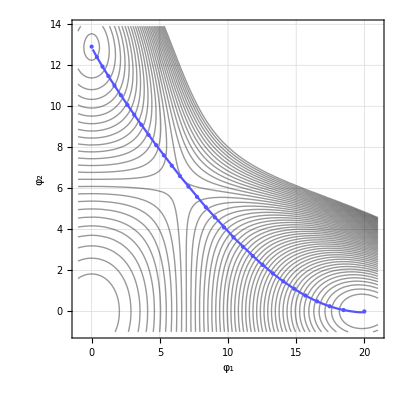
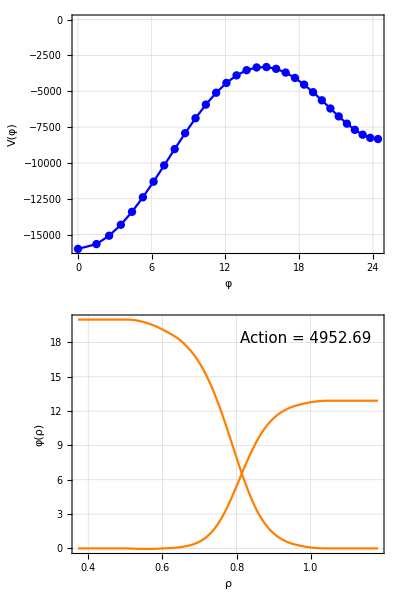

```mathematica
bounce=PB2["Bounce"];
R=Last@PB2["BounceParameters"];
markers=bounce/@R;
pBounce2 =Show[ParametricPlot[bounce[ρ],{ρ,0,1},PlotStyle->Lighter@Blue]];
Potential1D = ListPlot[Transpose@{PB2["PathLongitudinal"],PB2["Potential"]},
	Joined->True,
	Mesh->All,
	PlotStyle->Blue,
	Frame->True,
	FrameLabel->{"φ","V(φ)"},
	LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],
	GridLines->Automatic,
	GridLinesStyle->GrayLevel[.85],	
	ImageSize->Medium,	
	PlotRange->All,
	Axes->False];
plot2 = {Show[contourV,pBounce2 ,PlotRange->All,ImageSize->400,Epilog->{(*{Text[Style[Row[{"Action = ",PB2["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightGreen]},{Text[Style["Case B",10,15,"Times New Roman"],Scaled[{0.85,0.84}],Background->LightRed]},*)PointSize[Medium],Lighter@Blue,Point[markers]}],
Column[{Potential1D,BouncePlot[PB2,ImageSize->Medium,Epilog->{Text[Style[Row[{"Action = ",PB2["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightGreen]}]}]};Row[plot2]
```

## Three Field Potential

### The Potential

#### Minima

```mathematica
{typeV,Extrema3,parameters3}=Block[{μ1=40,μ2=100,μ3=120,λ1=.1,λ2=.2,λ3=.3,α1=2,α2=2.1,α3=1.2,ϵ1 =100,ϵ2 = 150,ϵ3 = 100,V,Φ,ϕ1,ϕ2,ϕ3,dV,d2V,sols,typeV,Extrema,ExtremaAnsatz,singEig ,parameters3},
V[ϕ_] := -μ1 (ϕ[[1]])^2-μ2 (ϕ[[2]])^2-μ3 (ϕ[[3]])^2 +λ1 (ϕ[[1]])^4+λ2 (ϕ[[2]])^4+λ3 (ϕ[[3]])^4+ α1 (ϕ[[1]])^2 (ϕ[[2]])^2+α2 (ϕ[[1]])^2 (ϕ[[3]])^2+α3 (ϕ[[2]])^2 (ϕ[[3]])^2 +ϵ1 ϕ[[1]] +ϵ2 ϕ[[2]] +ϵ3 ϕ[[3]] ;
Φ = {ϕ1,ϕ2,ϕ3};
dV = D[V[Φ],{Φ}];
d2V = D[V[Φ],{Φ},{Φ}];
ExtremaAnsatz={{0.,-15.8113883,0.},{6.54653671,-5.976143,0.},{20.,0.,0.}};
(*Find new minima*)
sols = Table[FindRoot[dV,Transpose@{Φ,ExtremaAnsatz[[i]]}],{i,1,3}];
d2V = D[V[Φ],{Φ},{Φ}]/.sols;
singEig =Table[DeleteDuplicates@Sign[Eigenvalues@d2V[[i]]],{i,1,3}];
(*Classify type of minima*)
typeV = Table[If[Length@singEig[[i]] >1,"Saddle",If[singEig[[i,1]] >0,"Minimum","Maximum"]],{i,1,3}];
Extrema = Φ/.sols;
parameters3 = {μ1,μ2,μ3,λ1,λ2,λ3,α1,α2,α3,ϵ1,ϵ2,ϵ3} ;
{typeV,Extrema,parameters3}//Chop
];
Row[{"type of Minima: ",typeV}]
```

type of Minima: {Minimum,Saddle,Minimum}

#### Potential

```mathematica
Potential3[ϕ_]:=Block[{V,μ1,μ2,μ3,λ1,λ2,λ3,α1,α2,α3,ϵ1,ϵ2,ϵ3},
{μ1,μ2,μ3,λ1,λ2,λ3,α1,α2,α3,ϵ1,ϵ2,ϵ3}=parameters3;
V = -μ1 (ϕ[[1]])^2-μ2 (ϕ[[2]])^2-μ3 (ϕ[[3]])^2 +λ1 (ϕ[[1]])^4+λ2 (ϕ[[2]])^4+λ3 (ϕ[[3]])^4+ α1 (ϕ[[1]])^2 (ϕ[[2]])^2+α2 (ϕ[[1]])^2 (ϕ[[3]])^2+α3 (ϕ[[2]])^2 (ϕ[[3]])^2 +ϵ1 ϕ[[1]] +ϵ2 ϕ[[2]] +ϵ3 ϕ[[3]] ];
φs3 = {φ1,φ2,φ3};
```

#### Plot

```mathematica
plotPotential =Block[{extremaV,triangleV,potential3,plotZ,plot},
triangleV = Graphics3D[{Darker[Red],Thickness[.005],Line[Extrema3]}];
extremaV=ListPointPlot3D[ Extrema3 ,PlotStyle->{Directive[ Orange,PointSize[.02]]}];
potential3  =Show[RegionPlot3D[Potential3[{Φ1,Φ2,Φ3}]<-1500,{Φ1,-1.5,22},{Φ2,-22,2},{Φ3,-2.8,1},PlotStyle->{Directive[Darker[Orange],Opacity[0.5]],Directive[Lighter[Blue],Opacity[0.5]]},Mesh->None,AxesLabel->{"ϕ_1","ϕ_2","ϕ_3"},LabelStyle->Directive[Black,FontSize->25, FontFamily->"Times New Roman",FontSlant->Plain],PlotRange->All,Lighting->"Neutral",Background->None],
triangleV,extremaV];
plotZ =Show[ContourPlot[Potential3[{Φ1,Φ2,-2.5}],{Φ1,-1.5,22},{Φ2,-22,2},Contours->60,GridLines->Automatic,Axes->False,GridLinesStyle->Directive[Dashed,GrayLevel[.85]],ContourStyle->Opacity[0.4],ImageSize->Medium,PlotRangePadding->0,Frame->False,LabelStyle->Directive[Black,FontSize->25, FontFamily->"Times New Roman",FontSlant->Plain]],ListPlot[Transpose@Transpose[Extrema3][[{1,2}]],PlotStyle->{Directive[ Orange,PointSize[.02]]}],ListPlot[Transpose@Transpose[Extrema3][[{1,2}]],PlotStyle->{Red},Joined->True]];
plot = {Show[potential3,PlotRange->All,BoxRatios->{1,1,1},ImageSize->400],plotZ } ];
contourZ[plotZ_Graphics]:=Block[{levelZ,c,projectionZ},
c =PlotRange/.plotZ[[2]];
levelZ=-3.5;
projectionZ=Graphics3D[{Texture[plotZ],EdgeForm[],Polygon[{{c[[1,1]],c[[2,1]],levelZ},{c[[1,2]],c[[2,1]],levelZ},{c[[1,2]],c[[2,2]],levelZ},{c[[1,1]],c[[2,2]],levelZ}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral",ImageSize->400]];
```

### Bounce

```mathematica
Block[{time},
{time,PB3} =FindBounce[Potential3[φs3],φs3,{Extrema3[[1]],Extrema3[[3]]},"InitialFieldValue"->Extrema3[[2]],"AccuracyBounce"->10]//AbsoluteTiming;
Row[{"Total time consumed = ",time," s."}]    ]
PB3
```

Total time consumed = 0.393036 s.

-7                                    -6                                      -7
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                        -7            -6            -7                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                   3.37813 10               2             1.8829 10               2              3.50825 10               2                                               0.00652734             2             0.0117211             2              0.000734696             2                                           0.0321342            2             0.0427506             2              0.0000501049             2                                            0.073825             2             0.0822932             2              0.00413349             2                                           0.125579             2             0.121862             2              0.0122093            2                                            0.18065             2             0.154158             2             0.0238999              2                                            0.232349             2             0.172914             2             0.0385183             2                                            0.274361             2             0.172781             2             0.0551142             2                                           0.300928             2             0.149305             2             0.072563             2                                            0.306957             2             0.0989493             2            0.0896282             2                                           0.288123            2             0.0191619            2             0.105014            2                                           0.240964             2             0.0915394             2            0.117413            2                                           0.162984             2           0.233453             2             0.125552             2                                            0.0527599             2             0.405559             2             0.128247             2                                            0.089923             2             0.605371            2           0.124457             2                                             0.263935             2             0.828759             2             0.113348             2                                           0.466637            2              1.06977             2             0.0943759             2                                           0.693698             2            1.32044             2             0.0673682             2                                           0.938909             2            1.57064             2             0.0326354             2                                           1.194            2            1.80803             2             0.00891124             2                                           1.44852             2         2.01815             2             0.0556338             2                                           1.68992             2            2.18509             2              0.105069             2                                           1.90441            2            2.29278             2             0.154008              2                                           2.07822             2            2.32658             2             0.198778              2                                           2.19772             2            2.27356             2           0.235391             2                                          2.24824            2            2.12233             2            0.259454             2                                          2.21205             2            1.86321            2            0.266022             2                                           2.06354             2            1.48831             2            0.249214             2                                           1.75357             2            0.988617             2             0.200706             2                                           1.10029             2            0.432157             2             0.111579              2
BounceFunction[<|Action -> 275.447, BounceParameters -> {{{-0.0840005, -15.6692, -0.427032}, {-0.792502, -16.9416, -0.347252}, {-2.2663, -18.7275, -0.386653}, {-4.08804, -20.4554, -0.569462}, {-5.9858, -21.9063, -0.865595}, {-7.76112, -22.9474, -1.24246}, {-9.26537, -23.4932, -1.66781}, {-10.3873, -23.4896, -2.11101}, {-11.046, -22.9076, -2.54358}, {-11.1858, -21.7394, -2.9395}, {-10.7745, -19.9967, -3.27554}, {-9.80056, -17.7105, -3.5316}, {-8.2727, -14.93, -3.69107}, {-6.21887, -11.7231, -3.74129}, {-3.68591, -8.17599, -3.674}, {-0.739372, -4.39337, -3.48591}, {2.53674, -0.498112, -3.17927}, {6.04023, 3.36964, -2.76255}, {9.65134, 7.05428, -2.25105}, {13.2342, 10.3885, -1.66751}, {16.6397, 13.2, -1.04235}, {19.7119, 15.3244, -0.413228}, {22.3027, 16.6253, 0.177907}, {24.2901, 17.0118, 0.689816}, {25.5787, 16.4401, 1.0846}, {26.0896, 14.9107, 1.32796}, {25.7491, 12.4732, 1.38974}, {24.4666, 9.23555, 1.24459}, {22.0663, 5.36606, 0.868962}, {17.7668, 1.70379, 0.282379}}, {{5.16304, 30.5031, -6.82538}, {24.3879, 65.0288, -8.99019}, {45.594, 90.7255, -8.42326}, {65.4949, 109.601, -6.42623}, {82.8921, 122.902, -3.7115}, {97.1996, 131.293, -0.674329}, {108.142, 135.262, 2.41975}, {115.633, 135.239, 5.37878}, {119.715, 131.632, 8.05975}, {120.526, 124.856, 10.3561}, {118.28, 115.34, 12.191}, {113.251, 103.537, 13.513}, {105.768, 89.9174, 14.2941}, {96.2002, 74.9784, 14.5281}, {84.9587, 59.236, 14.2294}, {72.4853, 43.2233, 13.4332}, {59.248, 27.4842, 12.1942}, {45.7335, 12.5647, 10.5867}, {32.4387, -1.00086, 8.70358}, {19.858, -12.7084, 6.65454}, {8.46618, -22.1134, 4.56331}, {-1.30789, -28.8723, 2.56176}, {-9.1316, -32.8005, 0.776678}, {-14.8126, -33.9053, -0.686636}, {-18.2863, -32.3641, -1.75088}, {-19.578, -28.4974, -2.36614}, {-18.7774, -22.765, -2.51144}, {-16.0084, -15.7751, -2.19807}, {-11.3616, -8.28404, -1.47087}, {-4.28745, -2.25835, -0.505743}}, {{-3.37813 10  , -1.8829 10  , 3.50825 10  }, {0.00652734, 0.0117211, -0.000734696}, {0.0321342, 0.0427506, -0.0000501049}, {0.073825, 0.0822932, 0.00413349}, {0.125579, 0.121862, 0.0122093}, {0.18065, 0.154158, 0.0238999}, {0.232349, 0.172914, 0.0385183}, {0.274361, 0.172781, 0.0551142}, {0.300928, 0.149305, 0.072563}, {0.306957, 0.0989493, 0.0896282}, {0.288123, 0.0191619, 0.105014}, {0.240964, -0.0915394, 0.117413}, {0.162984, -0.233453, 0.125552}, {0.0527599, -0.405559, 0.128247}, {-0.089923, -0.605371, 0.124457}, {-0.263935, -0.828759, 0.113348}, {-0.466637, -1.06977, 0.0943759}, {-0.693698, -1.32044, 0.0673682}, {-0.938909, -1.57064, 0.0326354}, {-1.194, -1.80803, -0.00891124}, {-1.44852, -2.01815, -0.0556338}, {-1.68992, -2.18509, -0.105069}, {-1.90441, -2.29278, -0.154008}, {-2.07822, -2.32658, -0.198778}, {-2.19772, -2.27356, -0.235391}, {-2.24824, -2.12233, -0.259454}, {-2.21205, -1.86321, -0.266022}, {-2.06354, -1.48831, -0.249214}, {-1.75357, -0.988617, -0.200706}, {-1.10029, -0.432157, -0.111579}}, 2, {0.00262132, 0.137925, 0.187645, 0.214922, 0.234398, 0.249858, 0.262895, 0.274337, 0.284672, 0.294217, 0.30319, 0.311753, 0.320032, 0.328132, 0.336142, 0.344145, 0.352223, 0.360455, 0.368927, 0.377732, 0.386971, 0.396756, 0.407204, 0.418485, 0.430887, 0.44487, 0.461191, 0.481239, 0.508051, 0.550799, 0.704524}}, Dimensions -> 4, Domain -> {0., 0.704524}, InitialSegment -> 2, ImprovedBounce -> {-2.28164, {372.882, 339.373, 294.822, 242.58, 186.646, 129.928, 74.4873, 21.8146, -26.9813, -71.0515, -109.731, -142.489, -168.901, -188.631, -201.424, -207.107, -205.599, -196.931, -181.275, -159.002, -130.746, -97.4767, -60.4978, -21.3548, 18.1964, 56.057, 89.5814, 115.159, 133.624, 130.349, 0}, {-0.0447303, 6.51135, 18.7862, 29.443, 34.2353, 31.4942, 21.7569, 7.18826, -9.04303, -23.3737, -32.4057, -33.3961, -24.6584, -5.85504, 21.8358, 55.7052, 91.6714, 124.637, 149.067, 159.795, 153.037, 127.469, 85.0398, 31.0426, -26.525, -77.8699, -112.697, -121.889, -104.559, -50.5706, 0}, {-20.4389, -17.1234, -14.0568, -11.3071, -8.61609, -5.97948, -3.43018, -1.00734, 1.25084, 3.30883, 5.13405, 6.69686, 7.97059, 8.93164, 9.55992, 9.83954, 9.76002, 9.31816, 8.52101, 7.39035, 5.96923, 4.33082, 2.59294, 0.878689, -0.716834, -2.11026, -3.22242, -3.97646, -4.51301, -4.82443, 0}, {0., -0.00501374, -0.00693073, -0.00441805, -0.00502848, -0.0129306, -0.0228686, -0.0182966, 0.0274533, 0.14779, 0.377882, 0.748592, 1.27982, 1.97378, 2.80883, 3.73456, 4.66925, 5.5008, 6.09278, 6.29762, 5.97885, 5.04193, 3.46817, 1.33718, -1.16477, -3.73961, -5.97907, -7.37162, -7.66957, -5.57515, 0}, {0., 0.0154008, -0.000434195, -0.00154819, -0.00181986, -0.00190662, -0.00193245, -0.00193356, -0.0019233, -0.00190731, -0.00188819, -0.00186719, -0.00184487, -0.00182141, -0.00179675, -0.00177065, -0.00174264, -0.00171206, -0.00167788, -0.00163865, -0.00159217, -0.00153521, -0.00146294, -0.00136797, -0.00123774, -0.00104878, -0.000752236, -0.000229502, 0.00088867, 0.00451887, 0.0747449}}, Iterations -> 3, Segments -> 30, Method -> DerrickFindRoot, Path -> {{-0.134976, -15.9533, -0.374093}, {0.0111189, -15.1072, -0.552782}, {0.242806, -14.3446, -0.680799}, {0.522622, -13.6409, -0.773282}, {0.837721, -12.9687, -0.844175}, {1.18106, -12.3171, -0.89907}, {1.54817, -11.6802, -0.941102}, {1.93594, -11.0544, -0.972262}, {2.3421, -10.4376, -0.993914}, {2.76491, -9.8283, -1.00704}, {3.20298, -9.22559, -1.0124}, {3.65519, -8.62901, -1.01056}, {4.12056, -8.03838, -1.00199}, {4.59825, -7.45383, -0.987094}, {5.08748, -6.87575, -0.966199}, {5.58747, -6.30482, -0.939614}, {6.09743, -5.74202, -0.907635}, {6.61644, -5.18871, -0.870561}, {7.14337, -4.64671, -0.828725}, {7.67671, -4.11846, -0.782522}, {8.21437, -3.60711, -0.732454}, {8.75327, -3.11685, -0.679189}, {9.28904, -2.65295, -0.623626}, {9.81779, -2.22, -0.566717}, {10.338, -1.82061, -0.509247}, {10.8495, -1.45671, -0.451915}, {11.3526, -1.13044, -0.395437}, {11.8489, -0.844277, -0.340555}, {12.3423, -0.601273, -0.288032}, {12.8432, -0.404588, -0.23848}, {13.422, -0.28804, -0.193469}}, PathLongitudinal -> {0, 0.877014, 1.68431, 2.44717, 3.19296, 3.93156, 4.66791, 5.40472, 6.14356, 6.88531, 7.63042, 8.37902, 9.13101, 9.88607, 10.6437, 11.4031, 12.1632, 12.9227, 13.6798, 14.4319, 15.1756, 15.9061, 16.6169, 17.3027, 17.9611, 18.5914, 19.1937, 19.7692, 20.3217, 20.8621, 21.4543}, Bounce -> (Piecewise[{{{-0.0840005, -15.6692, -0.427032}, #1 < 0.00262132}, {{-0.0840005 - ------------ + 5.16304 #1 , -15.6692 - ----------- + 30.5031 #1 , -0.427032 + ------------ - 6.82538 #1 }, 0.00262132 <= #1 < 0.137925}, {{-0.792502 + ---------- + 24.3879 #1 , -16.9416 + --------- + 65.0288 #1 , -0.347252 - ----------- - 8.99019 #1 }, 0.137925 <= #1 < 0.187645}, {{-2.2663 + --------- + 45.594 #1 , -18.7275 + --------- + 90.7255 #1 , -0.386653 - ------------ - 8.42326 #1 }, 0.187645 <= #1 < 0.214922}, {{-4.08804 + -------- + 65.4949 #1 , -20.4554 + --------- + 109.601 #1 , -0.569462 + ---------- - 6.42623 #1 }, 0.214922 <= #1 < 0.234398}, {{-5.9858 + -------- + 82.8921 #1 , -21.9063 + -------- + 122.902 #1 , -0.865595 + --------- - 3.7115 #1 }, 0.234398 <= #1 < 0.249858}, {{-7.76112 + ------- + 97.1996 #1 , -22.9474 + -------- + 131.293 #1 , -1.24246 + --------- - 0.674329 #1 }, 0.249858 <= #1 < 0.262895}, {{-9.26537 + -------- + 108.142 #1 , -23.4932 + -------- + 135.262 #1 , -1.66781 + --------- + 2.41975 #1 }, 0.262895 <= #1 < 0.274337}, {{-10.3873 + -------- + 115.633 #1 , -23.4896 + -------- + 135.239 #1 , -2.11101 + --------- + 5.37878 #1 }, 0.274337 <= #1 < 0.284672}, {{-11.046 + -------- + 119.715 #1 , -22.9076 + -------- + 131.632 #1 , -2.54358 + -------- + 8.05975 #1 }, 0.284672 <= #1 < 0.294217}, {{-11.1858 + -------- + 120.526 #1 , -21.7394 + --------- + 124.856 #1 , -2.9395 + --------- + 10.3561 #1 }, 0.294217 <= #1 < 0.30319}, {{-10.7745 + -------- + 118.28 #1 , -19.9967 + --------- + 115.34 #1 , -3.27554 + -------- + 12.191 #1 }, 0.30319 <= #1 < 0.311753}, {{-9.80056 + -------- + 113.251 #1 , -17.7105 - --------- + 103.537 #1 , -3.5316 + -------- + 13.513 #1 }, 0.311753 <= #1 < 0.320032}, {{-8.2727 + -------- + 105.768 #1 , -14.93 - -------- + 89.9174 #1 , -3.69107 + -------- + 14.2941 #1 }, 0.320032 <= #1 < 0.328132}, {{-6.21887 + --------- + 96.2002 #1 , -11.7231 - -------- + 74.9784 #1 , -3.74129 + -------- + 14.5281 #1 }, 0.328132 <= #1 < 0.336142}, {{-3.68591 - -------- + 84.9587 #1 , -8.17599 - -------- + 59.236 #1 , -3.674 + -------- + 14.2294 #1 }, 0.336142 <= #1 < 0.344145}, {{-0.739372 - -------- + 72.4853 #1 , -4.39337 - -------- + 43.2233 #1 , -3.48591 + -------- + 13.4332 #1 }, 0.344145 <= #1 < 0.352223}, {{2.53674 - -------- + 59.248 #1 , -0.498112 - ------- + 27.4842 #1 , -3.17927 + --------- + 12.1942 #1 }, 0.352223 <= #1 < 0.360455}, {{6.04023 - -------- + 45.7335 #1 , 3.36964 - ------- + 12.5647 #1 , -2.76255 + --------- + 10.5867 #1 }, 0.360455 <= #1 < 0.368927}, {{9.65134 - -------- + 32.4387 #1 , 7.05428 - ------- - 1.00086 #1 , -2.25105 + --------- + 8.70358 #1 }, 0.368927 <= #1 < 0.377732}, {{13.2342 - ----- + 19.858 #1 , 10.3885 - ------- - 12.7084 #1 , -1.66751 - ---------- + 6.65454 #1 }, 0.377732 <= #1 < 0.386971}, {{16.6397 - ------- + 8.46618 #1 , 13.2 - ------- - 22.1134 #1 , -1.04235 - --------- + 4.56331 #1 }, 0.386971 <= #1 < 0.396756}, {{19.7119 - ------- - 1.30789 #1 , 15.3244 - ------- - 28.8723 #1 , -0.413228 - -------- + 2.56176 #1 }, 0.396756 <= #1 < 0.407204}, {{22.3027 - ------- - 9.1316 #1 , 16.6253 - ------- - 32.8005 #1 , 0.177907 - -------- + 0.776678 #1 }, 0.407204 <= #1 < 0.418485}, {{24.2901 - ------- - 14.8126 #1 , 17.0118 - ------- - 33.9053 #1 , 0.689816 - -------- - 0.686636 #1 }, 0.418485 <= #1 < 0.430887}, {{25.5787 - ------- - 18.2863 #1 , 16.4401 - ------- - 32.3641 #1 , 1.0846 - -------- - 1.75088 #1 }, 0.430887 <= #1 < 0.44487}, {{26.0896 - ------- - 19.578 #1 , 14.9107 - ------- - 28.4974 #1 , 1.32796 - -------- - 2.36614 #1 }, 0.44487 <= #1 < 0.461191}, {{25.7491 - ------- - 18.7774 #1 , 12.4732 - ------- - 22.765 #1 , 1.38974 - -------- - 2.51144 #1 }, 0.461191 <= #1 < 0.481239}, {{24.4666 - ------- - 16.0084 #1 , 9.23555 - ------- - 15.7751 #1 , 1.24459 - -------- - 2.19807 #1 }, 0.481239 <= #1 < 0.508051}, {{22.0663 - ------- - 11.3616 #1 , 5.36606 - -------- - 8.28404 #1 , 0.868962 - -------- - 1.47087 #1 }, 0.508051 <= #1 < 0.550799}, {{17.7668 - ------- - 4.28745 #1 , 1.70379 - -------- - 2.25835 #1 , 0.282379 - -------- - 0.505743 #1 }, 0.550799 <= #1 < 0.704524}}, {13.422, -0.28804, -0.193469}] & ), Potential -> {-14905.3, -14678.4, -14223.3, -13601., -12839.7, -11966.8, -11009.4, -9994.87, -8950.37, -7902.48, -6876.56, -5896.29, -4983.07, -4155.51, -3428.96, -2815., -2321.03, -1949.88, -1699.53, -1562.91, -1527.88, -1577.46, -1690.5, -1843.86, -2015.61, -2186.82, -2342.33, -2471.2, -2566.9, -2626.82, -2649.68}|>]
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                               2                                      2                                      2                                                                       2                                    2                                     2                                                                  2                                  2                                     2                                                                   2                                   2                                    2                                                                 2                                  2                                    2                                                                2                                 2                                   2                                                                  2                                  2                                   2                                                                 2                                  2                                   2                                                                2                                  2                                  2                                                                 2                                   2                                  2                                                                2                                  2                                 2                                                               2                                   2                                 2                                                               2                                2                                  2                                                                  2                                  2                                  2                                                                 2                                  2                               2                                                                  2                                  2                                  2                                                                2                                  2                                  2                                                                2                                 2                                  2                                                                2                                 2                                  2                                                               2                              2                                  2                                                                 2                             2                                  2                                                                2                                2                                  2                                                                2                               2                                 2                                                                 2                                2                                 2                                                                 2                                2                               2                                                               2                               2                                2                                                               2                                2                               2                                                                2                                2                                2                                                                2                                2                                  2                                                                2                                2                                  2
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                             #1                                     #1                                     #1                                                                      #1                                   #1                                    #1                                                                 #1                                 #1                                    #1                                                                  #1                                  #1                                   #1                                                                #1                                 #1                                   #1                                                               #1                                #1                                  #1                                                                 #1                                 #1                                  #1                                                                #1                                 #1                                  #1                                                               #1                                 #1                                 #1                                                                #1                                  #1                                 #1                                                               #1                                 #1                                #1                                                              #1                                  #1                                #1                                                              #1                               #1                                 #1                                                                 #1                                 #1                                 #1                                                                #1                                 #1                              #1                                                                 #1                                 #1                                 #1                                                               #1                                 #1                                 #1                                                               #1                                #1                                 #1                                                               #1                                #1                                 #1                                                              #1                             #1                                 #1                                                                #1                            #1                                 #1                                                               #1                               #1                                 #1                                                               #1                              #1                                #1                                                                #1                               #1                                #1                                                                #1                               #1                              #1                                                              #1                              #1                               #1                                                              #1                               #1                              #1                                                               #1                               #1                               #1                                                               #1                               #1                                 #1                                                               #1                               #1                                 #1

### Plot

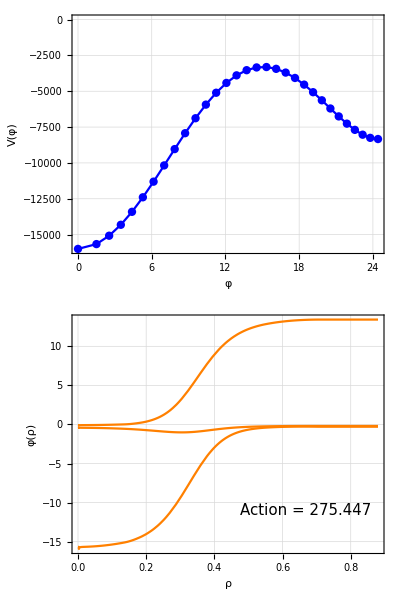
-Graphics3D--Graphics-

```mathematica
pBounce3 = BouncePlot[PB3,ImageSize->Medium,Epilog->{Text[Style[Row[{"Action = ",PB3["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.18}],Background->LightGreen]}];
bounce=PB3["Bounce"];
R=Last@PB3["BounceParameters"];
markers=bounce/@R;
pPathBounce3 =Show[ParametricPlot3D[bounce[ρ],{ρ,0,1},PlotStyle->Cyan]];
PlotBounce2DProjection =Show[ParametricPlot[bounce[ρ][[{1,2}]],{ρ,0,1},PlotStyle->Cyan]];
pPotential1D = ListPlot[Transpose@{PB2["PathLongitudinal"],PB2["Potential"]},
	Joined->True,
	Mesh->All,
	PlotStyle->Blue,
	Frame->True,
	FrameLabel->{"φ","V(φ)"},
	LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],
	GridLines->Automatic,
	GridLinesStyle->GrayLevel[.85],	
	ImageSize->Medium,	
	PlotRange->All,
	Axes->False];
plot3 = {Show[{plotPotential[[1]],contourZ[Show[plotPotential[[2]],Show[PlotBounce2DProjection]]],pPathBounce3 },PlotRange->All,ImageSize->400],
Column[{pPotential1D,pBounce3}]};Row[plot3]
```

## All Plots

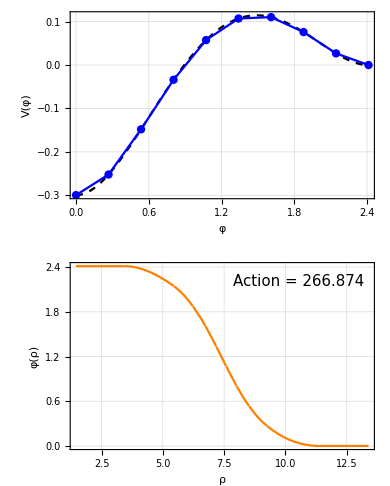
-Graphics--Graphics--Graphics-     -Graphics3D--Graphics-

```mathematica
PLOTS = Magnify[Row[Flatten[{GraphicsGrid[Transpose@{plot1}],plot2,"     ",plot3,"    "}]],.6]
```

```mathematica
Export[ FileNameJoin[{FileNameTake[NotebookDirectory[],{1,-2}],"ExaplesBounces.png"}],PLOTS ];
```

## Dynamical Examples

## >Single Field Potential

### Plot

```mathematica
ListPlotBounce[pts_List]:=Block[{PB,φV,plot},
	φV = Transpose[pts];
	PB =FindBounce[Null,Null,{φV[[1,1]],φV[[1,-1]]},"AnsatzPath"->φV[[1]],"AnsatzV"->φV[[2]]]//Quiet;
	Plot[PB["Bounce"][ρ],{ρ,0,14},
	ImageSize->Medium,
	PlotRange->{{0,14},{-.1,1.1}},
Epilog->{Text[Style[Row[{"Action = ",PB["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.2}],Background->LightGreen]},		
	Frame->True,
		FrameLabel->{"ρ","φ(ρ)"},
		LabelStyle->Directive[Black,FontSize->17, 
FontFamily->"Times New Roman",FontSlant->Plain],
		GridLines->Automatic,
		PlotStyle->Orange]  ];
DynamicModule[{pts ={{0.,-0.4},{0.15,-0.3},{0.25,0.3},{0.5,0.7},{0.75,0.3},{1,0}},d=4,ptsT,PB,plot},
ptsT =Transpose[pts];
Row[{LocatorPane[Dynamic[pts],Dynamic[   ListPlot[pts,Joined->True,Mesh->All,PlotRange->{{-0.1,1.1},{Min[ptsT[[2]]] 2,Max[ptsT[[2]]]1.5}},Frame->True,
FrameLabel->{"φ","V(φ)"},GridLines->Automatic,GridLinesStyle->GrayLevel[.85],ImageSize->Medium,MeshStyle->PointSize[Large],LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],PlotStyle->Darker[Blue],Axes->False]      ],Appearance->None],Dynamic[ListPlotBounce[pts]] }]]
```

## >Two Field Potential

### Plot

```mathematica
DynamicModule[{μ,λ,αs,ϵ,μλαϵ,Extrema,plot,abort,Action,Potential2,dV,d2V,plots,ϕ1,ϕ2,ϕs,d=4,PB2 ,plot2,pBounce2,Potential1D,pPathBounce2,Extrema0={{0,12.9099},{6.259,6.00687},{20.,0.}}},
Manipulate[
 μλαϵ={{μ1,μ2},{λ1,λ2},α,{ϵ1,ϵ2}};
(*========================================*)
Potential2[ϕ_]:=μλαϵ⟦3⟧ ϕ⟦1⟧^2 ϕ⟦2⟧^2-ϕ⟦1⟧^2 μλαϵ⟦1,1⟧-ϕ⟦2⟧^2 μλαϵ⟦1,2⟧+ϕ⟦1⟧^4 μλαϵ⟦2,1⟧+ϕ⟦2⟧^4 μλαϵ⟦2,2⟧+ϕ⟦1⟧ μλαϵ⟦4,1⟧+ϕ⟦2⟧ μλαϵ⟦4,2⟧; 
dV[ϕ_]:= {2 μλαϵ⟦3⟧ ϕ⟦1⟧ ϕ⟦2⟧^2-2 ϕ⟦1⟧ μλαϵ⟦1,1⟧+4 ϕ⟦1⟧^3 μλαϵ⟦2,1⟧+μλαϵ⟦4,1⟧,2 μλαϵ⟦3⟧ ϕ⟦1⟧^2 ϕ⟦2⟧-2 ϕ⟦2⟧ μλαϵ⟦1,2⟧+4 ϕ⟦2⟧^3 μλαϵ⟦2,2⟧+μλαϵ⟦4,2⟧};
d2V[ϕ_]:= {{2 μλαϵ⟦3⟧ ϕ⟦2⟧^2-2 μλαϵ⟦1,1⟧+12 ϕ⟦1⟧^2 μλαϵ⟦2,1⟧,4 μλαϵ⟦3⟧ ϕ⟦1⟧ ϕ⟦2⟧},{4 μλαϵ⟦3⟧ ϕ⟦1⟧ ϕ⟦2⟧,2 μλαϵ⟦3⟧ ϕ⟦1⟧^2-2 μλαϵ⟦1,2⟧+12 ϕ⟦2⟧^2 μλαϵ⟦2,2⟧}};
ϕs ={ϕ1,ϕ2};
(*========================================*) 
Quiet[Extrema = Table[ϕs/.Chop@FindRoot[dV[ϕs],Transpose@{ϕs,Extrema0[[i]]}],{i,3}];
PB2  =FindBounce[Potential2[ϕs],ϕs,Extrema[[{1,3}]],"InitialFieldValue"->Extrema[[2]], "Dimensions"->d, "Segments"->n,"MaxIterationsPathDeformation"->2 ,Gradient->dV[ϕs],Hessian->d2V[ϕs]];
pBounce2 = BouncePlot[PB2["Bounce"],ImageSize->Medium]; 
pPathBounce2 =ParametricPlot[PB2["Bounce"][ρ],{ρ,0,10},PlotStyle->Cyan];
Potential1D = ListPlot[Transpose@{PB2["PathLongitudinal"],PB2["Potential"]},
	Joined->True,
	Mesh->All,
	PlotStyle->Blue,
	Frame->True,
	FrameLabel->{"φ","V(φ)"},
	LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],
	GridLines->Automatic,
	GridLinesStyle->GrayLevel[.85],	
	ImageSize->Medium,	
	PlotRange->All,
	Axes->False];
(*========================================*) 
plots =Show[ ContourPlot[ Potential2[{ϕ1,ϕ2}],{ϕ1,-5,25},{ϕ2,-5,25},PlotRange->{Automatic,5000},GridLines->Automatic,Contours->10,GridLinesStyle->Directive[Dashed,GrayLevel[.85]],ContourStyle->Opacity[0.4],FrameLabel->{"φ_1","φ_2"},LabelStyle->Directive[Black,FontSize->20, FontFamily->"Times New Roman",FontSlant->Plain],PlotPoints->2,MaxRecursion->3] , ListPlot[ Extrema ,PlotStyle->{PointSize[.015],Darker@Red} ],pPathBounce2];     ];
(*========================================*) 
Row[{Show[plots,ImageSize->Medium],Column[{Potential1D,BouncePlot[PB2,ImageSize->Medium,Epilog->{Text[Style[Row[{"Action = ",PB2["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightGreen]}]}]}]
,{{μ1,80.,"μ_1"},70,120,Appearance->"Labeled"},{{μ2,100.,"μ_2"},70,120,Appearance->"Labeled"},{{λ1,.1,"λ_1"},.05,.8,Appearance->"Labeled"},{{λ2,.2,"λ_2"},.05,.8,Appearance->"Labeled"},{{α,3.,"α"},0.7,8,Appearance->"Labeled"},{{ϵ1,0.,"ϵ_1"},0,900,Appearance->"Labeled"},{{ϵ2,0.,"ϵ_2"},0,900,Appearance->"Labeled"},{{n,20,"n"},10,30,1,Appearance->"Labeled"},Paneled->False ]]
```